# 1 Explicit Surfaces

## Plot3D and ContourPlot

If we assign the output of a function of two variables f(x,y) to be a third variable, z=f(x,y), then the set of points in 3D define a surface. For example, z = x^2+ y^2 defines a paraboloid. This explicit surface can be visualized using the Plot3D function:

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2},PlotTheme->"Scientific"]
```

-Graphics3D-

The first argument is the function, and the next arguments define the domain - here we use a simple square domain, but it is straight-forward to define more interesting domains. Notice that the graphical object comes with the ability to rotate it.

It is often helpful to visualize a surface by drawing the contours defined by holding z constant. For example, if we define z=1 in the equation for the paraboloid we obtain x^2+ y^2 = 1, which we know to be the equation of a circle of radius 1, centered at the origin. Choosing different values of z will define circles of radius √z. We already met ContourPlot in the earlier notebook, but we will use it a little differently here:

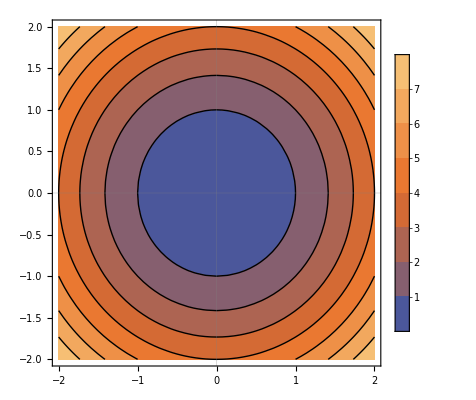

```mathematica
ContourPlot[x^2+y^2,{x,-2,2},{y,-2,2},PlotTheme->"Scientific",PlotLegends->Automatic]
```

In this case, ContourPlot has chosen contour levels for us, and even colored the regions between them - we’ve used the PlotLegends option to provide a color legend on the side. It is straight-forward to plot specific contour levels using the Contours option:

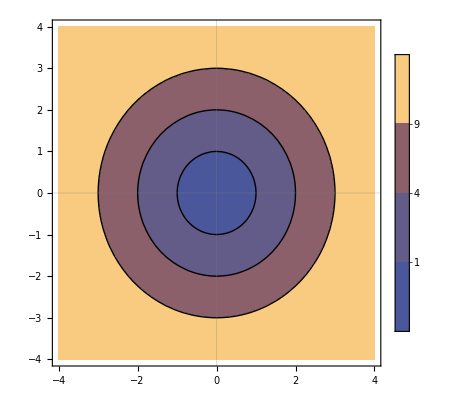

```mathematica
ContourPlot[x^2+y^2,{x,-4,4},{y,-4,4},PlotTheme->"Scientific",PlotLegends->Automatic, Contours->{1,4,9}]
```

Notice how we defined three contour levels at z = 1, 4, and 9 and the result is a set of circles of radius 1, 2, and 3 as expected. We also had to increase the size of the domain so that the contour level at z=9 was visible.

## Exercises

1. Use Plot3D, ContourPlot and Manipulate to visualize the elliptic paraboloid z = c(x^2/a^2 + y^2/b^2) for different values of a, b, and c. What features of the surface do a, b, and c control?

```mathematica
Manipulate[Plot3D[c*((x^2)/(a^2)+(y^2)/(b^2)),{x,-2,2},{y,-2,2},PlotTheme->"Scientific"],{a,-5,5,Appearance->"Labeled"}, {b,-5,5,Appearance->"Labeled"}, {c,-5,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[ContourPlot[c*((x^2)/(a^2)+(y^2)/(b^2)),{x,-2,2},{y,-2,2},PlotTheme->"Scientific",PlotLegends->Automatic],{a,-5,5,Appearance->"Labeled"}, {b,-5,5,Appearance->"Labeled"}, {c,-5,5,Appearance->"Labeled"}]
```

A and B control the height and how “skinny” the paraboloid is in the x and x directions respectively
C controls the concavity in the y direction, as well as height.

2. Use Plot3D, ContourPlot and Manipulate to visualize the hyperbolic paraboloid z = c(x^2/a^2 - y^2/b^2) for different values of a, b, and c. What features of the surface do a, b, and c control?

```mathematica
Manipulate[Plot3D[c*((x^2)/(a^2)-(y^2)/(b^2)),{x,-2,2},{y,-2,2},PlotTheme->"Scientific"],{a,-5,5,Appearance->"Labeled"}, {b,-5,5,Appearance->"Labeled"}, {c,-5,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[ContourPlot[c*((x^2)/(a^2)-(y^2)/(b^2)),{x,-2,2},{y,-2,2},PlotTheme->"Scientific",PlotLegends->Automatic],{a,-5,5,Appearance->"Labeled"}, {b,-5,5,Appearance->"Labeled"}, {c,-5,5,Appearance->"Labeled"}]
```

A controls the height of the parabola and how concave it is in the x direction.
B controls the height/concavity in the z direction
C controls whether the paraboloid is concave up in the x or z direction

# 2 Implicit Surfaces

## ContourPlot3D and ContourPlot

A surface in three dimensions can also be implicitly defined by a function of three variables. For example, the equation for a unit sphere centered at the origin is

x^2+y^2+z^2 -1 = 0

The left hand side can be thought of as a function of three variables, f(x,y,z), and the set of points where f=0 defines the unit sphere. We can use the ContourPlot3D function to visualize:

```mathematica
ContourPlot3D[x^2 + y^2 + z^2 - 1 == 0, {x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Scientific"]
```

-Graphics3D-

Notice that the formulation is similar to ContourPlot, but now we define a domain in three dimensions. Introducing parameters, and using Manipulate or Animate can be accomplished as before.

We would still like to be able to take “slices” through this surface and plot the resulting contour levels in 2D. For example, let’s say we want to look at the slices at different values of z. We could use the With function to do this:

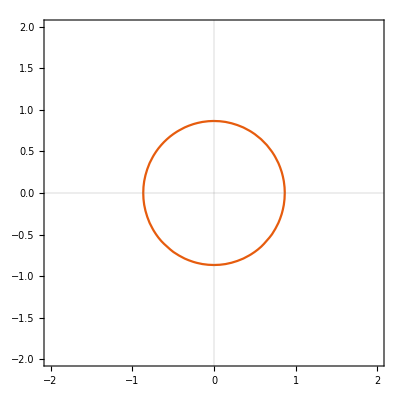

```mathematica
With[{z=0.5},
ContourPlot[x^2+y^2+z^2-1==0,{x,-2,2},{y,-2,2},PlotTheme->"Scientific"]]
```

Notice how we have deployed the ContourPlot function from before, and simply evaluated the expression with z=0.5 - the result is a circle as expected. If we prefer, we could use Manipulate to generate contour levels at various values of z:

```mathematica
Manipulate[ContourPlot[x^2+y^2+z^2-1==0,{x,-2,2},{y,-2,2},PlotTheme->"Scientific"],{z,0.1,0.9,Appearance->"Labeled"}]
```

and we see that every slice results in a circular contour as expected. If we prefer, we could take slices through the surface at different values of x or y instead. For slices in the y-plane:

```mathematica
Manipulate[ContourPlot[x^2+y^2+z^2-1==0,{x,-2,2},{z,-2,2},PlotTheme->"Scientific"],{y,0.1,0.9,Appearance->"Labeled"}]
```

Notice that we had to redefine the domain, and the manipulate variable, and again every slice is a circle as expected.

There are lots of implicit surfaces, but a particularly important group is the quadratic (or quadric) surfaces, defined by the equation:

A x^2+ B y^2+ C z^2+D y z + E z x + F x y + G x + H y + I z + J = 0

where A, B, C, D, E, F, G, H, I, and J are all arbitrary constants, some of which may be zero.

## Exercises

3. Use ContourPlot3D and ContourPlot to visualize the ellipsoid defined by  x^2/a^2+y^2/b^2+ z^2/c^2-1=0 for different values of a, b, and c. What features of the ellipsoid do a, b, and c control? Visualize and describe the slices in the x-plane, y-plane, and z-plane.

```mathematica
Manipulate[ContourPlot3D[(x^2)/(a^2)+(y^2)/(b^2)+ (z^2)/(c^2) - 1 == 0, {x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Scientific"],{a,0.1,5,Appearance->"Labeled"}, {b,0.1,5,Appearance->"Labeled"}, {c,0.1,5,Appearance->"Labeled"}]
```

A controls the length of the shape in the x direction
B controls the length of the shape in the y direction
C controls the length of the shape in the z direction
Cross sections in all directions are ellipses whose proportions are controlled by the values of A, B, and C

```mathematica
a=1;
b =2;
c =2;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)+ (z^2)/(c^2) - 1 == 0,{z,-2,2},{y,-2,2},PlotTheme->"Scientific", Axes->True, AxesLabel->{z,y}],{x,0.1,0.9,Appearance->"Labeled"}]
```

```mathematica
a=1;
b =2;
c =2;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)+ (z^2)/(c^2) - 1 == 0,{x,-2,2},{z,-2,2},PlotTheme->"Scientific",Axes->True, AxesLabel->{x,z}],{y,0.1,0.9,Appearance->"Labeled"}]
```

```mathematica
a=1;
b =2;
c =2;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)+ (z^2)/(c^2) - 1 == 0,{x,-2,2},{y,-2,2},PlotTheme->"Scientific", Axes->True, AxesLabel->{x,y}],{z,0.1,0.9,Appearance->"Labeled"}]
```

4. Use ContourPlot3D and ContourPlot to visualize the double cone defined by x^2/a^2+y^2/b^2- z^2/c^2=0 for different values of a, b, and c. What features of the double cone do a, b, and c control? Visualize and describe the slices in the x-plane, y-plane, and z-plane.

```mathematica
Manipulate[ContourPlot3D[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)== 0, {x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Scientific"],{a,0.1,5,Appearance->"Labeled"}, {b,0.1,5,Appearance->"Labeled"}, {c,0.1,5,Appearance->"Labeled"}]
```

A controls the length of the shape in the x direction.
B controls the length of the shape in the y direction.
C controls the “curviness”/concavity of the shape. Aka how quickly the shape flares out at the top and bottom.
Cross sections in the x direction look like parabolas that are reflected over the top and bottom
Cross sections in the y direction are hourglass shapes. Just like the reflected parabolas the x direction but flipped 90 degrees.
Cross sections in the z direction are ellipses

```mathematica
a=0.5;
b =0.5;
c =1;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)== 0,{z,-2,2},{y,-2,2},PlotTheme->"Scientific",Axes->True, AxesLabel->{z,y}],{x,0.1,0.9,Appearance->"Labeled"}]
```

```mathematica
a=0.5;
b =0.5;
c =1;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)== 0,{x,-2,2},{z,-2,2},PlotTheme->"Scientific",Axes->True, AxesLabel->{x,z}],{y,0.1,0.9,Appearance->"Labeled"}]
```

```mathematica
a=0.5;
b =0.5;
c =1;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)== 0,{x,-2,2},{y,-2,2},PlotTheme->"Scientific",Axes->True, AxesLabel->{x,y}],{z,0.1,0.9,Appearance->"Labeled"}]
```

5. Use ContourPlot3D and ContourPlot to visualize the hyperboloid of one sheet defined by x^2/a^2+y^2/b^2- z^2/c^2-1=0 for different values of a, b, and c. What features of the hyperboloid do a, b, and c control? Visualize and describe the slices in the x-plane, y-plane, and z-plane.

```mathematica
Manipulate[ContourPlot3D[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)-1== 0, {x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Scientific"],{a,0.1,5,Appearance->"Labeled"}, {b,0.1,5,Appearance->"Labeled"}, {c,0.1,5,Appearance->"Labeled"}]
```

A controls the length of the shape in the x direction.
B controls the length of the shape in the y direction.
C controls the “curviness”/concavity of the shape. Aka how quickly the shape flares out at the top and bottom.
Cross sections in the x direction look like parabolas that are reflected over the top and bottom
Cross sections in the y direction are hourglass shapes. Just like the reflected parabolas the x direction but flipped 90 degrees.
Cross sections in the z direction are ellipses

```mathematica
a=01;
b =1;
c =1;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)-1== 0,{z,-2,2},{y,-2,2},PlotTheme->"Scientific",Axes->True, AxesLabel->{z, y}],{x,0.1,0.9,Appearance->"Labeled"}]
```

```mathematica
a=1;
b =1;
c =1;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)-1== 0,{x,-2,2},{z,-2,2},PlotTheme->"Scientific",Axes->True, AxesLabel->{x,z}],{y,0.1,0.9,Appearance->"Labeled"}]
```

```mathematica
a=1;
b =1;
c =1;
Manipulate[ContourPlot[(x^2)/(a^2)+(y^2)/(b^2)- (z^2)/(c^2)-1== 0,{x,-2,2},{y,-2,2},PlotTheme->"Scientific",Axes->True, AxesLabel->{x,y}],{z,0.1,0.9,Appearance->"Labeled"}]
```

# 3 Parametric Surfaces

## ParametricPlot3D

Finally, a more general representation of a surface involves expressing it’s coordinates in terms of two independent variables or parameters as follows

x = f(u,v), y = g(u,v), z = h(u,v),  u ϵ [a,b], v ϵ [c,d]

Each value of (u,v) defines a point with coordinates (f(u,v),g(u,v),h(u,v)). If we collect all the points defined by (u,v) in the specified domain, then we get a parametric surface. For example, the definition

x=sin(u)cos(v),y=sin(u)sin(v),z = cos(u), u ϵ [0,π], v ϵ [0,2π]

defines a unit sphere. In Mathematica we visualize parametric surfaces using the ParametricPlot3D function:

```mathematica
ParametricPlot3D[{Sin[u]*Cos[v],Sin[u]*Sin[v],Cos[u]},{u,0,Pi},{v,0,2*Pi},PlotTheme->"Scientific"]
```

-Graphics3D-

Again the first argument is the set of functions enclosed in braces - these are the x and y and z coordinates of the surface. The second and third arguments are the domain of definition. u and v can be interpreted as the angle running north-south, and east-west respectively.

It’s often helpful to visualize the parametric curves defined by holding one of the parameters fixed, and varying the other. For example, let’s visualize the parametric curves defined by holding v fixed:

```mathematica
Manipulate[ParametricPlot3D[{Sin[u]*Cos[v],Sin[u]*Sin[v],Cos[u]},{u,0,Pi},PlotTheme->"Scientific",PlotRange->{{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}}],{v,0,2*Pi}]
```

Notice that we used PlotRange to fix the domain, otherwise it dynamically changes as you use Manipulate.You can see from this that each different v defines a line of longitude. Repeating this while holding u fixed shows that each different u defines a line of latitude:

```mathematica
Manipulate[ParametricPlot3D[{Sin[u]*Cos[v],Sin[u]*Sin[v],Cos[u]},{v,0,2*Pi},PlotTheme->"Scientific",PlotRange->{{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}}],{u,0,Pi}]
```

Wouldn’t it be nice if we could visualize these “coordinate” curves with the surface of the sphere being plotted too? Go on, you can do it!

## Exercises

6. Lookup the parametric equations that define an ellipsoid, and use ParametricPlot3D to verify them. What is the interpretation of the parameters u and v in this case?

```mathematica
Clear[a, b, c]
Manipulate[ParametricPlot3D[{a*Sin[u]*Cos[v],b*Sin[u]*Sin[v],c*Cos[u]},{u,0,Pi},{v,0,2*Pi},PlotTheme->"Scientific"],{a,1,4,Appearance->"Labeled"}, {b,1,4,Appearance->"Labeled"}, {c,1,4,Appearance->"Labeled"}]
```

Each value of u, v defines a point with the x, y, z coordinates x = a*Sin[u]*Cos[v], b*Sin[u]*Sin[v], c*Cos[u]

6. Lookup the parametric equations that define an hyperboloid of one sheet, and use ParametricPlot3D to verify them. What is the interpretation of the parameters u and v in this case?

```mathematica
Manipulate[ParametricPlot3D[{a*Sqrt[1+u^2]*Cos[v],a*Sqrt[1+u^2]*Sin[v],c*u},{u,-Pi,Pi},{v,0,2*Pi},PlotTheme->"Scientific"],{a,1,4,Appearance->"Labeled"}, {c,1,4,Appearance->"Labeled"}]
```

Each value of u, v defines a point with the x, y, z coordinates x = a*Sqrt[1+u^2]*Cos[v], y = a*Sqrt[1+u^2]*Sin[v], z = c*u

8. Use ParametricPlot3D and Manipulate to visualize the following parametric surface

x = (a + r cos(u))cos(v), y = (a+r cos(u))sin(v), z = r sin(u)

with r<a and u ϵ [0,2π], v ϵ [0,2π]. Describe the surface and interpret the variables and parameters.

```mathematica
Manipulate[ParametricPlot3D[{(a+r*Cos[u])*Cos[v],(a+r*Cos[u])*Sin[v],r*Sin[u]},{u,-Pi,Pi},{v,0,2*Pi},PlotTheme->"Scientific"],{a,1,4,Appearance->"Labeled"}, {r,1,4,Appearance->"Labeled"}]
```

Each value of u, v defines a point with the x, y, z coordinates x = (a+r*Cos[u])*Cos[v], y = (a+r*Cos[u])*Sin[v], z = r*Sin[u]

9. Find an interesting parametric surface, and implement it in Mathematica. Interpret the parameter and any variables.

Helicoid:

```mathematica
Manipulate[ParametricPlot3D[{u*Cos[v],u*Sin[v],a*v},{u,-Pi,Pi},{v,0,2*Pi},PlotTheme->"Scientific"],{a,1,16,Appearance->"Labeled"}]
```

Each value of u, v defines a point with the x, y, z coordinates x = u*Cos[v], y = u*Sin[v], z = a*v

Bonus: I present to you the 3D Olin logo standing up straight instead of leaning over. Alternative title: squished doughnut.

```mathematica
Manipulate[ParametricPlot3D[{(a+r*Cos[u])*Cos[v],(a+b*Cos[u])*Sin[v],c*Sin[u]},{u,-Pi,Pi},{v,0,2*Pi},PlotTheme->"Scientific"],{a,1,16,Appearance->"Labeled"}, {b,1,8,Appearance->"Labeled"},{c,1,8,Appearance->"Labeled"},{r,1,8,Appearance->"Labeled"}]
```